```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-10;a=1;αSch=2.;V=-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&[r];VCou=-α/r;
Vs1=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]/.{c1->-44.29438139648679};
Vs2=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]/.{c2->-39.94772282822709,d1->3.265518446170086};
```

```mathematica
EigenEnergy[V_,αSch_]:=
Module[{min=1.*10^-19,max=2000,wpc=50,acg=30,sol,ef,evShifted,evnew,steps=∞,stepfraction=10^-2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
(*Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*)},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=Riffle[(ev-shift),evShifted]];
Print[evShifted];*)
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,(*MaxStepFraction->stepfraction,*)WorkingPrecision->wpc,AccuracyGoal->acg];
evnew=e/.#&/@
ParallelTable[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.95 SetPrecision[evShifted[[n]],3],1.05 SetPrecision[evShifted[[n]],3]},WorkingPrecision->wpc,AccuracyGoal->acg,StepMonitor:>PrintTemporary[e]],{n,20}]
]
```

```mathematica
energyV=EigenEnergy[V,αSch]
```

{-1.33726,-0.186431,-0.0710568,-0.0374069,-0.0230508,-0.0156183,-0.0112778,-0.0085243,-0.00666879,-0.00535928,-0.00440079,-0.00367821,-0.00312002,-0.00267989,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.00129368}

1

3

5

7

9

10

11

12

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) u[r$789]-0.5 u''[r$789]==e$788 u[r$789],u'[2000]==-1.×10^-19,u[2000]==1.×10^-19},{},{},{},{}}) is less than WorkingPrecision (50.).

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000034887457824470612792201409891311685041370805345469; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00002966365740271339593921474602715355120748217604462; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000034114242446763206071166947432573527709928413546841; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000014341984084309386978547802223177839010321714228361; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000023938787723602304731506697482052236284847291880384; unable to continue.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000070571930876489273491272895787924763528207924397005; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000069495324452314232361277016398252710742967557157303; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0034943

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00010221140232804899645890362444930817256293729201465; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00509131

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000075350210197369695807760102160800175378186340216694; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00418075

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000046653506897253165945279454470476429952154566086713; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00011857519087520938042549264675281813598867915594622; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0107139

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00011009175543977657487452846948158729834123910057888; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00633535

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000030967123460495226518908065107171682316121480576014; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00003591183915985298589052148359860959522718463581868; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00418076

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000028512741484454380764708554739753329690986562555366; unable to continue.

-0.00349432

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00017299279808443463150572849475273346438577478384725; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0218983

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00509132

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000014339156292433595935874078302446649778475320680306; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0107139

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000024205244759969793216254644281265616788683270255466; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00633535

-0.0044008

-0.00367822

-0.00535928

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000065955765354390922816643979891968549096877370789221; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.0218983

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00024249042864606711713662891558921134728482937119685; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0675039

-0.0044008

-0.00367822

-0.00666879

-0.00535928

-0.0112778

-0.0218983

-0.0044008

-0.00666879

-0.00535929

-0.0112778

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000046653506897253165945279454470476429952154566086713; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00666881

-0.0230509

-0.0112778

-0.003678219946522848313869014091892

-0.004400800989843452713790039609876

-0.0112778

-0.0230509

-0.003678219960704503367309491459882

-0.005359292793683845951280275698991

-0.004400800989842510227620919729945

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000018447981383178282553187154056222414936422857634718; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.003678219960705176388796550071972

-0.005359292793644056844457845841364

-0.004400800989842510231323095558573

-0.003678219960705176388796533335561

-0.0230509

-0.005359292793644057808002845975583

-0.004400800989842510231323095801332

-0.006668809823052094729045613519247

-0.004400800989842510231323095801332

-0.06750392784298338293855359726905

-0.006668809822562327012118503186876

-0.01127779477751940373497774317002

-0.023051

-0.004400800989842510231323095801561

13

-0.006668809822562366917808176531329

-0.0053592927936440578080028466644261120883388857174555

-0.01127779477753463308039423752676

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00003839541326999910670617098677885127266087544358707; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.006668809822562366917808549270656

-0.0053592927936440578080028466644261022263299415987704

-0.07105676615050882113593179356954

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000086721993454306082140098009041943831128784099190093; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00296402

14

-0.006668809822562366917808549270656

-0.0053592927936440578080028466644261022235558181264556

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00003768049679667624806622347466605451936751360491326; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00296406

15

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000036530398024093274188722146581139963600128387524623; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.006668809822562366917808549270718

-0.011277794777534633085953433890002731966767870807612

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000080977214734287015270912116581706116799345892433212; unable to continue.

-0.02305097182694811758230102327616

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0025459

-0.00312004

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000046991282998204095641627487503576137286427382590365; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.07105676615050882113593179356954

-0.011277794777534633085953433875850633479038545417146

-0.00312004

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000038204156264147984606565535020099971710627646917566; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00254595

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000075273402292051629835378120431439262762255920132049; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00221039

-0.02305097182706901485808306097118

-0.00267992

8

-0.00312003

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000036993105783377978047846806404779721374350696773772; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00221047

16

-0.02305097182706901499266764864014

-0.00267992

-0.00312003

-0.00232677

-0.07105676620183473738563380024391

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000025300505319472930672413655513226433395305349153966; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-1.2704

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000046047049290044777966016218216565988173283813663689; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00232677

-0.0026799

-0.02305097182706901499266764955955

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000067878288052691135429405438293358716518432544715583; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00809809

-0.00193709

-0.0026799

-0.00232673

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000045913862246422267118396198724197079439850762579105; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00193719

-0.003120030569799089187332796768715

-0.00809809

-0.02305097182706901499266764955955

-0.07105746642208059032164616251837

-0.00232673

-0.00203909

-0.0085243

-0.00203909

-0.002679897893559875926561275605309

-0.003120030569799089095153345231991008840529489662111

-0.0085243

-0.00203904

-0.0031200305697990890951533453748029502628926695787916

-0.07105746377772401748617297984373

-0.002326732490108473095508090366934

-0.0031200305697990890951533453748037560759089907238442

-0.00203904

-0.00852432

-0.0026798978935598757150766563187212446549774174260647

-0.0031200305697990890951533453748037560782035906598343

6

-0.0026798978935598757150766620217659180075437554179546

-0.0031200305697990890951533453748037560770562906918392

-0.00852433

-0.07105746378765325594762605725659

-0.0023267324901084712731141282456984110926662239564079

-0.0026798978935598757150766620217659180075437554179546

-0.0031200305697990890951533453748037560764826407078417

-0.0023267324901084712731143344570534890930570718589165

-0.002039044122714921396938292375012

17

-0.0026798978935598757150766620109270994383903625115287

-0.0023267324901084712731143344891567082844356970448912

-0.0026798978935598757150766619619688872968935031066275

-0.0148374

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000041435279573102728490555187168660258181439925949892; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000018447981383178282553187154056222414936422857634718; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.07105746378765339701555918503264

-0.0023267324901084712731143344891567082844356970448912

-0.0026798978935598757150766619374897812261450734041769

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000061865103691970049190708714928813137223910397878995; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00171151

-0.008524333164520949204789879161126

-0.0023267324901084712731143344922174038977633565091867

-0.0148374

-0.0026798978935598757150766619252502281907708585529516

-0.0020390441227149137139585683476851275487796738819321

-0.0023267324901084712731143344911333303243709053192512

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000042647920528344147568832966392081168985582530943445; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00171165

-0.008524333164522088605326416586723

-0.0026798978935598757150766619191304516730837511273389

-0.0020390441227149137139613738420907464733235084159376

-0.0023267324901084712731143344896701517370749268519331

-0.07105746378765339701555918614621

-0.00180166

-0.0148398

-0.0026798978935598757150766619160705634142401974145326

-0.0020390441227149137139613738423083960537378430610045

-0.0023267324901084712731143344894134300107553119484122

-0.0026798978935598757150766619145406192848184205581294

-0.00180166

-0.0020390441227149137139613738423077793297975222883417

-0.0023267324901084712731143344894134300107553119484122

-0.0148398

-0.0026798978935598757150766619137756472201075321299279

18

-0.0085243331645220886054141342747096288895475395674922

-0.00180158

-0.0023267324901084712731143344894075546306912587610085

-0.0026798978935598757150766619137756472201075321299279

-0.07105746378765339701555918614621

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000052142562490778490372479804709818380544976349984429; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0023267324901084712731143344893463118891433816288301

-0.0085243331645220886054141339637710126742760155841508

-0.0148788

-0.00180159

-0.0026798978935598757150766619137744888382555695804373

-0.0023267324901084712731143344893156905183694430627409

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000055491255001276539906308748763012463635206879268805; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00152316

-0.0085243331645220886054141339637730430220882880138131

-0.0026798978935598757150766619135838250130038287481322

-0.0156195

-0.0023267324901084712731143344893156905183694430627409

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000050058953043602418836045912469052548518578112512131; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00152335

-0.0026798978935598757150766619135838250130038287481322

19

-0.0023267324901084712731143344893152427286493909350923

-0.0026798978935598757150766619135835511352374169765554

-0.00160342

-0.0156195

-0.001801592784043863550852426769211

-0.0023267324901084712731143344893078112808159323573943

ParametricNDSolve::nderr: Error test failure at r$789 == 0.00004595044880439806187729538695278174707605623305597; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0026798978935598757150766619135360221178076876542675

-0.00160342

-0.0023267324901084712731143344893040955568992030685453

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000065169264617932578727784669848291702012847130566661; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.00136427

-0.0156195

-0.0026798978935598757150766619135360221178076876542675

-0.0023267324901084712731143344893022376949408384241208

-0.00160331

-0.0026798978935598757150766619135359555082710110790744

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000045200443467320297880472080460323013277135576915926; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

-0.0018015927840438462645092178809476816049825478389172

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00136452

-0.0023267324901084712731143344893022376949408384241208

-0.00160333

-0.0156184

-0.0026798978935598757150766619135359555082710110790744

-0.0018015927840438462645264724004581621303636172844037

-0.0014362

-0.0023267324901084712731143344893022126608619552829677

-0.002679897893559875715076661913535922297207795860585

-0.0018015927840438462645264723701343317472699661877858

-0.0023267324901084712731143344893017607124118056924381

-0.0014362

-0.0156184

-0.0018015927840438462645264723701343317472699661877858

-0.002679897893559875715076661913535922297207795860585

-0.07105746378765339701555918614621345996471280571946

-0.0023267324901084712731143344893017607124118056924381

-0.00143605

-0.0018015927840438462645264723701343317472699661877858

-0.0026798978935598757150766619135359057383076264640652

-0.0023267324901084712731143344893017546410518872861616

-0.00160332767053418057470737245751

-0.0018015927840438462645264723425628816831858688347356

-0.0026798978935598757150766619135359057383076264640652

-0.00143608

-0.0023267324901084712731143344893016446896193090916675

-0.001603327670533971790253836190889

-0.0018015927840438462645264723425628816831858688347356

-0.0026798978935598757150766619135359041946840578206138

-0.0023267324901084712731143344893016446896193090916675

-0.071057463787653397015559186146213460186524036408954

-0.0018015927840438462645264723425628816831858688347356

-0.0026798978935598757150766619135356216003805928141562

-0.002326732490108471273114334489301643213654635519894

-0.0018015927840438462645264723425628816831858688347356

-0.01561839001932825710117214157435

-0.0016033276705339717907609105582839431280490438725736

-0.0026798978935598757150766619135356216003805928141562

-0.002326732490108471273114334489301643213654635519894

-0.0018015927840438462645264723425628816808561707017728

-0.001436077605768367989116929273052

-0.001603327670533971790760910552353850158579741460207

-0.0026798978935598757150766619135356212043831288172544

-0.0023267324901084712731143344893016424971077359024803

-0.0018015927840438462645264723425628816808561707017728

-0.01561839001932659835319289049279

-0.001436077605767294682850687673561

4

-0.001603327670533971790760910552353850158579741460207

-0.0026798978935598757150766619135356212043831288172544

-0.0023267324901084712731143344893016424971077359024803

-0.0018015927840438462645264723425628815548127561871843

-0.0016033276705339717907609104757318893298172564474216

-0.0026798978935598757150766619135356210071156373321136

-0.0023267324901084712731143344893016421476443379050763

-0.0018015927840438462645264723425628815772554034925551

-0.0016033276705339717907609105125450056974066393636492

-0.0026798978935598757150766619135356210071156373321136

-0.0018015927840438462645264723425628816612433257586766

-0.0023267324901084712731143344893016358140438098674475

-0.001436077605767294688735300648682250725512093329525

-0.0016033276705339717907609105174226193621534092629884

-0.0026798978935598757150766619135356209086701645347788

-0.0018015927840438462645264723425628816610612192569807

-0.0023267324901084712731143344893016358140438098674475

-0.0016033276705339717907609105348882347603665753615977

-0.0014360776057672946887353006001734598680602729989042

-1.270399777199777036074124225706

-0.0026798978935598757150766619135356033945654902414405

-0.0018015927840438462645264723425628816401552919412983

-0.0023267324901084712731143344893016357290271378197741

-0.0016033276705339717907609105348882347603665753615977

-0.015618390019326598359214796639364041765237354679605

-0.0014360776057672946887353005962693096981433522723652

-0.0355366

-0.0026798978935598757150766619135356033945654902414405

-0.0018015927840438462645264723425628816401552919412983

-0.0023267324901084712731143344893016357290271378197741

-0.0016033276705339717907609105365146682293659163298464

-0.0014360776057672946887353005964953992865028339403503

-0.015618390019326598359214796485228419523922384711774

-0.0026798978935598757150766619135356033700232428457229

-0.0018015927840438462645264723425628816470837971221605

-0.0016033276705339717907609105436210424594731584109023

-0.0023267324901084712731143344893016356876600019074756

-0.0014360776057672946887353005964953992865028339403503

-0.0018015927840438462645264723425628816470622459037694

-0.0026798978935598757150766619135355990037681979702471

-0.0016033276705339717907609105430493896505977778188345

-0.0014360776057672946887353005965027726249109562356835

-0.0023267324901084712731143344893016356876600019074756

-0.0355366

20

-0.0018015927840438462645264723425628816446964932369121

-0.0016033276705339717907609105430493896505977778188345

-0.0026798978935598757150766619135355968206406755325093

-0.0014360776057672946887353005965079461675554219668374

-0.0023267324901084712731143344893016356675770902468444

-0.0018015927840438462645264723425628816446964932369121

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000052976000518575366771840203383128069860892411432936; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.0016033276705339717907609105431030228738189030152448

-0.0014360776057672946887353005965079461675554219668374

-0.0026798978935598757150766619135355957290769143136403

-0.0023267324901084712731143344893016356675770902468444

-0.0016033276705339717907609105431030228738189030152448

-0.0018015927840438462645264723425628816447982118202449

-0.0355366

-0.0014360776057672946887353005965079461675554219668374

-0.0026798978935598757150766619135355951832950337042059

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000058804679599909785108828882350293006759041038941645; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.001229

-0.0023267324901084712731143344893016356577825213715955

-0.0016033276705339717907609105431188222887969045148095

-0.0018015927840438462645264723425628816450108302156075

-0.0014360776057672946887353005965080011421776600242127

-0.0026798978935598757150766619135355951832950337042059

-0.0023267324901084712731143344893016354802599512152188

ParametricNDSolve::nderr: Error test failure at r$789 == 0.000052216626854481982802530223931742097631099670326229; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-19} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.00122932

-0.0016033276705339717907609105431394492673070871128015

-0.0018015927840438462645264723425628816451171394132889

-0.0014360776057672946887353005965080011421776600242127

-0.0026798978935598757150766619135355951825312057858282

-0.0023267324901084712731143344893016354802599512152188

-0.00129384

-0.0016033276705339717907609105431497627565621784117975

-0.0018015927840438462645264723425628816451702940121295

-0.0374069

-0.0014360776057672946887353005965080158738252986077414

-0.0026798978935598757150766619135355951825312057858282

-0.0023267324901084712731143344893016354778770486475989

-0.0016033276705339717907609105431497627565621784117975

-0.0018015927840438462645264723425628816451968713115499

-0.0014360776057672946887353005965080623160871789439356

-0.00129384

-0.0026798978935598757150766619135355951821504458652616

-0.0016033276705339717907609105431497627565621784117975

-0.0023267324901084712731143344893016354778770486475989

-0.00180159278404384626452647234256288164521015996126

-0.0014360776057672946887353005965080855372181191120328

-0.0374069

-0.00129366

-0.0026798978935598757150766619135355951821504458652616

-0.0016033276705339717907609105431499950530175830927855

-0.00180159278404384626452647234256288164521015996126

-0.0023267324901084712731143344893016354767175833034405

-0.0014360776057672946887353005965080855372181191120328

-0.0026798978935598757150766619135355951819605562564423

-0.0016033276705339717907609105431506457072842947773566

-0.00180159278404384626452647234256288164521015996126

-0.0023267324901084712731143344893016354767175833034405

-0.0014360776057672946887353005965080870706839154575182

-0.0012937

-0.0016033276705339717907609105431506457072842947773566

-0.0026798978935598757150766619135355951481348019927011

-0.00180159278404384626452647234256288164521015996126

-0.0023267324901084712731143344893016354761534142479155

-1.337262923368186307016003411263

-0.0014360776057672946887353005965080921092337523267998

-0.0016033276705339717907609105431507200634625046872134

-0.0374069

-0.0026798978935598757150766619135355951312219248608306

-0.00180159278404384626452647234256288164521015996126

-0.0023267324901084712731143344893016354761534142479155

-0.0014360776057672946887353005965080921092337523267998

-0.0016033276705339717907609105431508455489400776534278

-0.0026798978935598757150766619135355951227654862948953

-0.0018015927840438462645264723425628816452102320712147

-0.0023267324901084712731143344893016354758789192602596

-0.0014360776057672946887353005965080924420266949086767

-0.0016033276705339717907609105431508455489400776534278

-0.0018015927840438462645264723425628816452103077399965

-0.0026798978935598757150766619135355951227654862948953

-0.001293695346843834774117065755661

-0.0023267324901084712731143344893016354709034932790781

-0.0014360776057672946887353005965080924420266949086767

-0.0374072

-0.0016033276705339717907609105431508582238894350732183

-0.0018015927840438462645264723425628816452103455743875

-0.0026798978935598757150766619135355951227536514136619

-0.001293695346842170409353000304928

-0.0014360776057672946887353005965080926609267934994587

-0.0023267324901084712731143344893016354709034932790781

-0.0016033276705339717907609105431508832577841496048766

-0.0018015927840438462645264723425628816452103644915829

-0.0026798978935598757150766619135355951227536514136619

-0.0014360776057672946887353005965080926609267934994587

-0.001293695346842170425601970698429

-0.0023267324901084712731143344893016354708367076598012

-0.0016033276705339717907609105431508957747315068707058

-0.0018015927840438462645264723425628816452103644915829

-0.0026798978935598757150766619135355951227477505398029

-0.0014360776057672946887353005965080927181308086448171

-0.0023267324901084712731143344893016354708367076598012

-0.0016033276705339717907609105431509020332051855036204

-0.0018015927840438462645264723425628816452103644915829

-0.0014360776057672946887353005965080929059767335556272

-0.0026798978935598757150766619135355951227477505398029

-0.0023267324901084712731143344893016354708042113199181

-0.0016033276705339717907609105431509051624420248200776

-0.0018015927840438462645264723425628816452103654767177

-0.0014360776057672946887353005965080929998996960110323

-0.0026798978935598757150766619135355951227448083593591

-0.0016033276705339717907609105431509051624420248200776

-0.0023267324901084712731143344893016354702152276470312

-0.0012936953468421704256019708962707211690001211295948

-0.00180159278404384626452647234256288164521036651042

-0.0014360776057672946887353005965080930468611772387348

-0.002679897893559875715076661913535595122220706617829

-0.0016033276705339717907609105431509051624420248200776

-0.0023267324901084712731143344893016354702152276470312

-0.00129369534684217042560197083107588336493656524927

-0.00180159278404384626452647234256288164521036651042

-0.0014360776057672946887353005965080930468611772387348

-0.0016033276705339717907609105431509052517786040972165

-0.0026798978935598757150766619135355951219586557470639

-0.002326732490108471273114334489301635470207321662828

-0.00129369534684217042560197083107588336493656524927

-0.0018015927840438462645264723425628816452103666772221

-0.0014360776057672946887353005965080930499634974990343

-0.0016033276705339717907609105431509052517786040972165

-0.03740716881702328688863445904644

-0.0026798978935598757150766619135355951219586557470639

-0.0023267324901084712731143344893016354700640287367079

-0.0018015927840438462645264723425628816452103668522466

-0.0012936953468421704256019708354080246472771616028472

-0.0014360776057672946887353005965080930601527076758102

-0.0016033276705339717907609105431509052517786040972165

-0.0026798978935598757150766619135355951219582890039121

-0.0018015927840438462645264723425628816452103668522466

-0.0023267324901084712731143344893016354699923822736478

-0.0012936953468421704256019708351988335093372910223687

-0.0014360776057672946887353005965080930601527076758102

-0.0016033276705339717907609105431509052517786040972165

-0.0026798978935598757150766619135355951218929596577967

-0.0018015927840438462645264723425628816452103668804892

-0.03740716881795222039663135801505

-0.0023267324901084712731143344893016354699923822736478

-0.0012936953468421704256019708354080246472771616028472

-0.0016033276705339717907609105431509052545898877586251

-0.0014360776057672946887353005965080930610636704766373

-1.337262923368186307016003411263

-0.0018015927840438462645264723425628816452103668804892

-0.0026798978935598757150766619135355951218929596577967

-0.0023267324901084712731143344893016354699914206146239

-0.0012936953468421704256019708354080246472771616028472

-0.0016033276705339717907609105431509052585258241195587

-0.0014360776057672946887353005965080930629009255954276

-0.0018015927840438462645264723425628816452103668900532

-0.0026798978935598757150766619135355951218928682286969

-0.0023267324901084712731143344893016354699739898283708

-0.0016033276705339717907609105431509052585258241195587

-0.0012936953468421704256019708354080246472771616028472

-0.0014360776057672946887353005965080930640741191798129

-0.0018015927840438462645264723425628816452103668900532

-0.002679897893559875715076661913535595121876581606718

-0.001603327670533971790760910543150905258917301622264

-0.0023267324901084712731143344893016354699739898283708

-0.0014360776057672946887353005965080930640741191798129

-0.0012936953468421704256019708354080246472771616028472

-0.0018015927840438462645264723425628816452103668900532

-0.0026798978935598757150766619135355951218684382957285

-0.001603327670533971790760910543150905258917301622264

-0.0023267324901084712731143344893016354699737558674441

-0.0014360776057672946887353005965080930641516209870416

-0.0012936953468421704256019708354047872007820338329319

-0.0018015927840438462645264723425628816452103668910984

-0.0026798978935598757150766619135355951218643666402338

-0.0016033276705339717907609105431509052591031093075857

-0.0023267324901084712731143344893016354699737558674441

-0.0014360776057672946887353005965080930641516209870416

-0.0018015927840438462645264723425628816452103668921952

-0.0012936953468421704256019708354047872007820338329319

-0.0016033276705339717907609105431509052594043281343652

-0.0026798978935598757150766619135355951218623308124864

-0.0014360776057672946887353005965080930641516209870416

-0.0023267324901084712731143344893016354699736420203683

-0.0018015927840438462645264723425628816452103668927435

-0.0012936953468421704256019708354047849824274283165544

-0.001603327670533971790760910543150905259554937547755

-0.0026798978935598757150766619135355951218613128986127

-0.037407168817952223791419321051712515282956181888067

-0.0018015927840438462645264723425628816452103668927435

-0.0014360776057672946887353005965080930641563314523056

-0.0023267324901084712731143344893016354699715785858562

-0.0012936953468421704256019708354047849824274283165544

-0.0016033276705339717907609105431509052596302422544499

-0.0026798978935598757150766619135355951218613128986127

-0.0018015927840438462645264723425628816452103668927435

-0.0014360776057672946887353005965080930641563314523056

-0.0023267324901084712731143344893016354699715785858562

-0.0012936953468421704256019708354047849824274283165544

-0.0016033276705339717907609105431509052596302422544499

-0.0026798978935598757150766619135355951218613114740308

-0.0018015927840438462645264723425628816452103668927435

-0.0014360776057672946887353005965080930641584983782695

-0.037407168817952223791419320785082901300199658669188

-0.0023267324901084712731143344893016354699715508881774

-0.001603327670533971790760910543150905259637164718622

-0.0012936953468421704256019708354047266478240699241047

-0.0018015927840438462645264723425628816452103668927435

-0.0014360776057672946887353005965080930641584983782695

-0.0026798978935598757150766619135355951218613114740308

-0.0023267324901084712731143344893016354699710488783888

-0.001603327670533971790760910543150905259637164718622

-0.0012936953468421704256019708354047601348457679259275

-0.0018015927840438462645264723425628816452103668927435

-0.0014360776057672946887353005965080930641593772584767

-0.0026798978935598757150766619135355951218613107637335

-0.0016033276705339717907609105431509052596412760315198

-0.0023267324901084712731143344893016354699707978734945

-0.0012936953468421704256019708354047433551883014349267

-0.0018015927840438462645264723425628816452103668927445

-0.0014360776057672946887353005965080930641622638606283

-0.0016033276705339717907609105431509052596412760315198

-0.0026798978935598757150766619135355951218613107637335

-0.0023267324901084712731143344893016354699706723710474

-0.0012936953468421704256019708354047474026776152347415

-0.0018015927840438462645264723425628816452103668927455

-0.0016033276705339717907609105431509052596426511768014

-0.0014360776057672946887353005965080930641637071617041

-0.0026798978935598757150766619135355951218613104095789

-0.0023267324901084712731143344893016354699706096198238

-0.0012936953468421704256019708354047505367936375260929

-0.0018015927840438462645264723425628816452103668927455

-0.0016033276705339717907609105431509052596447770120831

-0.0014360776057672946887353005965080930641637071617041

-0.0026798978935598757150766619135355951218613104095789

-0.0023267324901084712731143344893016354699706096198238

-0.0012936953468421704256019708354047517681875573153243

-0.0018015927840438462645264723425628816452103668927455

-1.337262923368186307016127836032

-0.0016033276705339717907609105431509052596458399297239

-0.0014360776057672946887353005965080930641638025069594

-0.0026798978935598757150766619135355951218613102329973

-0.0023267324901084712731143344893016354699706087775081

-0.0012936953468421704256019708354047517681875573153243

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

-0.0016033276705339717907609105431509052596458399297239

-0.0014360776057672946887353005965080930641641156596007

-0.0026798978935598757150766619135355951218612787778417

-0.0023267324901084712731143344893016354699705935108601

-0.0012936953468421704256019708354047517681875573153243

-0.0016033276705339717907609105431509052596459731526702

-0.0014360776057672946887353005965080930641641156596007

-0.002679897893559875715076661913535595121861263050264

-0.002326732490108471273114334489301635469970585877536

-0.0016033276705339717907609105431509052596459731526702

-0.0012936953468421704256019708354047517681875573153243

-0.0014360776057672946887353005965080930641641363466243

-0.002679897893559875715076661913535595121861263050264

-0.002326732490108471273114334489301635469970585877536

-0.0016033276705339717907609105431509052596460227466908

-0.0012936953468421704256019708354047517681875573153243

-0.0014360776057672946887353005965080930641641363466243

-0.002679897893559875715076661913535595121861263028253

-0.0016033276705339717907609105431509052596460227466908

-0.0023267324901084712731143344893016354699705857750732

-0.001293695346842170425601970835404751768956044189475

-0.0014360776057672946887353005965080930641641484957484

-0.0016033276705339717907609105431509052596460227466908

-0.0026798978935598757150766619135355951218612591073641

-0.0023267324901084712731143344893016354699705839179736

-0.0012936953468421704256019708354047517692648628211993

-0.0014360776057672946887353005965080930641641484957484

-0.0016033276705339717907609105431509052596460273939183

-0.0026798978935598757150766619135355951218612591073641

-0.0023267324901084712731143344893016354699705839179736

-0.0012936953468421704256019708354047517698056197010163

-0.0014360776057672946887353005965080930641641537669308

-0.0016033276705339717907609105431509052596460343987713

-0.0026798978935598757150766619135355951218612591018767

-0.0023267324901084712731143344893016354699705838930456

-0.0014360776057672946887353005965080930641641537669308

-0.0012936953468421704256019708354047517697947933435799

-0.0016033276705339717907609105431509052596460343987713

-0.0026798978935598757150766619135355951218612591018767

-0.0023267324901084712731143344893016354699705838930456

-0.0014360776057672946887353005965080930641641559045357

-0.0012936953468421704256019708354047517695704363755616

-0.0016033276705339717907609105431509052596460352710882

-0.0026798978935598757150766619135355951218612590991407

-0.0014360776057672946887353005965080930641641559045357

-0.0023267324901084712731143344893016354699705838809162

-0.0012936953468421704256019708354047517694582578915524

-0.0016033276705339717907609105431509052596460365861431

-0.0014360776057672946887353005965080930641641559045357

-0.0023267324901084712731143344893016354699705836610754

-0.0026798978935598757150766619135355951218612590991407

-0.0012936953468421704256019708354047517694374017349729

-0.0016033276705339717907609105431509052596460372436705

-0.0014360776057672946887353005965080930641641560683251

-0.0026798978935598757150766619135355951218612590977766

-0.0023267324901084712731143344893016354699705835511551

-0.0012936953468421704256019708354047517693917405712581

-0.0016033276705339717907609105431509052596460372436705

-0.0014360776057672946887353005965080930641641560683251

-0.002679897893559875715076661913535595121861258854773

-0.0023267324901084712731143344893016354699705835511551

-0.0016033276705339717907609105431509052596460373255514

-0.0012936953468421704256019708354047517693917405712581

-0.001436077605767294688735300596508093064164156134746

-1.337324703389670833991970250904

-0.0026798978935598757150766619135355951218612587332712

-0.0023267324901084712731143344893016354699705835511551

-0.0016033276705339717907609105431509052596460374489928

-0.0012936953468421704256019708354047517693793784785956

-0.001436077605767294688735300596508093064164156134746

-0.0016033276705339717907609105431509052596460375107135

-0.0023267324901084712731143344893016354699705835511551

-0.0026798978935598757150766619135355951218612587332712

-0.0012936953468421704256019708354047517693793784785956

-0.0014360776057672946887353005965080930641641561616815

-0.0016033276705339717907609105431509052596460375107135

-0.002326732490108471273114334489301635469970583551154

-0.0026798978935598757150766619135355951218612587332712

-0.0012936953468421704256019708354047517693794844636712

-0.0014360776057672946887353005965080930641641561616815

-0.0016033276705339717907609105431509052596460375183995

-0.0023267324901084712731143344893016354699705835511347

-0.0026798978935598757150766619135355951218612587332708

-0.0012936953468421704256019708354047517693798452431055

-0.0014360776057672946887353005965080930641641561726046

-0.0016033276705339717907609105431509052596460375183995

-0.0023267324901084712731143344893016354699705835511347

-0.0026798978935598757150766619135355951218612587332708

-0.0012936953468421704256019708354047517693798452431055

-0.0014360776057672946887353005965080930641641561726046

-0.0016033276705339717907609105431509052596460375212853

-0.0023267324901084712731143344893016354699705835511347

-0.0026798978935598757150766619135355951218612587332708

-0.0012936953468421704256019708354047517693798452431055

-0.0014360776057672946887353005965080930641641561770342

-0.001603327670533971790760910543150905259646037525636

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

-0.0012936953468421704256019708354047517693798452431055

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

-0.0014360776057672946887353005965080930641641561865412

-0.0016033276705339717907609105431509052596460375278113

-0.0014360776057672946887353005965080930641641561865412

-0.001603327670533971790760910543150905259646037528899

-0.0012936953468421704256019708354047517693798480132717

-0.0016033276705339717907609105431509052596460375294428

-0.0014360776057672946887353005965080930641641561874393

-0.0012936953468421704256019708354047517693798480132717

-0.0016033276705339717907609105431509052596460375297147

-0.001436077605767294688735300596508093064164156189367

-0.0012936953468421704256019708354047517693798480132717

-0.0016033276705339717907609105431509052596460375297147

-0.001436077605767294688735300596508093064164156189367

-0.0012936953468421704256019708354047517693798480132717

-0.0016033276705339717907609105431509052596460375297486

-0.0014360776057672946887353005965080930641641561895491

-0.0012936953468421704256019708354047517693798480132412

-0.0016033276705339717907609105431509052596460375297996

-0.0014360776057672946887353005965080930641641561895491

-0.0012936953468421704256019708354047517693798480129989

-0.0016033276705339717907609105431509052596460375298252

-0.001436077605767294688735300596508093064164156189623

-0.0016033276705339717907609105431509052596460375298252

-0.0012936953468421704256019708354047517693798480129989

-1.337320043722131439522142283518

-0.001436077605767294688735300596508093064164156189623

-0.0016033276705339717907609105431509052596460375298252

-0.0014360776057672946887353005965080930641641561896529

-0.0012936953468421704256019708354047517693798480130529

-0.0016033276705339717907609105431509052596460375298252

-0.0014360776057672946887353005965080930641641561897172

-0.0012936953468421704256019708354047517693798480130529

-0.0016033276705339717907609105431509052596460375298254

-0.0014360776057672946887353005965080930641641561897172

-0.0012936953468421704256019708354047517693798480130529

-0.0016033276705339717907609105431509052596460375298254

-0.0014360776057672946887353005965080930641641561897233

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

-0.0014360776057672946887353005965080930641641561897363

-0.0014360776057672946887353005965080930641641561897363

-0.0014360776057672946887353005965080930641641561897376

-0.0014360776057672946887353005965080930641641561897376

-0.0014360776057672946887353005965080930641641561897381

-0.0014360776057672946887353005965080930641641561897381

-0.0014360776057672946887353005965080930641641561897383

-0.0014360776057672946887353005965080930641641561897387

-0.0014360776057672946887353005965080930641641561897387

FindRoot::brdig: The root has been bracketed as closely as possible with 50. working digits but the function value exceeds the absolute tolerance 1.×10^-30.

-1.33732035760837812564417763401

-1.337320359282444671479985888794

-1.3373203592824395316897406648316317137900927577649

-1.3373203592824395317002733492873886202632321783803

-1.3373203592824395317002733527229352844050240605771

2

-0.177109

-0.1771092958015753338063547062479

-0.1771092958015803229270749270535

-0.1864308376858712611448228294589

-0.1864308376858712611448228294589

-0.1864308376865920253731373200574

-0.1864339755700314627937123049645

-0.1864339430936046653830484446318

-0.1864339434245507733282188332427

-0.1864339434245858658046162261368

-0.1864339434245858658046101402663

{-1.3373203592824395317002733527229347788773163834974,-0.18643394342458586580461014026520012960767959181077,-0.071057463787653397015559186146213460075618421064207,-0.037407168817952223791419320785082914812552397503258,-0.023050971827069014992667649559551992186200082372817,-0.015618390019326598359214796485228395551936502555052,-0.011277794777534633085953433875850633787048438658481,-0.0085243331645220886054141339637730416987511986614978,-0.0066688098225623669178085492707178551527432109838923,-0.005359292793644057808002846664426102224942879862613,-0.0044008009898425102313230958015611525007744261479554,-0.0036782199607051763887965333355605720436445162313596,-0.0031200305697990890951533453748037560767694656998405,-0.0026798978935598757150766619135355951218612587332708,-0.0023267324901084712731143344893016354699705835511346,-0.0020390441227149137139613738423077775770416522698864,-0.0018015927840438462645264723425628816452103668927455,-0.0016033276705339717907609105431509052596460375298254,-0.0014360776057672946887353005965080930641641561897387,-0.0012936953468421704256019708354047517693798480130529}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Dump_Test_eigenfunction_NDSolve_2_energyV.mx",energyV]
```

{{-1.3373203592824395317002733527229347788773163834974,-0.18643394342458586580461014026520012960767959181077,-0.071057463787653397015559186146213460075618421064207,-0.037407168817952223791419320785082914812552397503258,-0.023050971827069014992667649559551992186200082372817,-0.015618390019326598359214796485228395551936502555052,-0.011277794777534633085953433875850633787048438658481,-0.0085243331645220886054141339637730416987511986614978,-0.0066688098225623669178085492707178551527432109838923,-0.005359292793644057808002846664426102224942879862613,-0.0044008009898425102313230958015611525007744261479554,-0.0036782199607051763887965333355605720436445162313596,-0.0031200305697990890951533453748037560767694656998405,-0.0026798978935598757150766619135355951218612587332708,-0.0023267324901084712731143344893016354699705835511346,-0.0020390441227149137139613738423077775770416522698864,-0.0018015927840438462645264723425628816452103668927455,-0.0016033276705339717907609105431509052596460375298254,-0.0014360776057672946887353005965080930641641561897387,-0.0012936953468421704256019708354047517693798480130529}}

```mathematica
<<C:\\Users\\ASUS\\Documents\\Dump_Test_eigenfunction_NDSolve_2_energyV.mx
```

```mathematica
Flatten@Import["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedHQ_NDSolve.dat"]
```

{-1.3373203577743778777484998097,-0.18643394332774011967873561071,-0.071057463765681416850087674062,-0.037407168809596011660801031892,-0.023050971823032012263856091426,-0.01561839001707619878572351763,-0.011277794776154149484804536219,-0.0085243331636150573081138113356,-0.0066688098219347947110873233838,-0.0053592927931919616196373210951,-0.0044008009895061115267162099337,-0.0036782199604481319905959313028,-0.0031200305695982845354571364731,-0.0026798978934000301370515335496,-0.0023267324899791593742692184066,-0.0020390441226088289036420519245,-0.0018015927839557429811049162805,-0.0016033276704600044466081691919,-0.0014360776057045943945272295712,-0.001293695346788560431501052664}

```mathematica
(%5-%6)/(%6)
```

{1.127674192039931383×10^-9,5.194641297460800553×10^-10,3.092142471890941165×10^-10,2.233853134716434573×10^-10,1.751337323130938828×10^-10,1.440865269103171761×10^-10,1.224072284120475509×10^-10,1.064049562459455319×10^-10,9.410557857821036366×10^-11,8.435743405171559539×10^-11,7.644033561368537787×10^-11,6.988282401938934173×10^-11,6.435980520603143665×10^-11,5.96461448843969476×10^-11,5.557660771147538925×10^-11,5.2026736029425918×10^-11,4.89029952862646251×10^-11,4.61336416226881876×10^-11,4.36607979673270316×10^-11,4.14394271680719789×10^-11}

```mathematica
eigenfunV=Range@20;
```

```mathematica
AbsoluteTiming[eigenfunV[[1]]=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],(*f'[r2]==1,f[r2]==r2*)f[r1]==r2,f'[r1]==-r2},f,{r,r1,0},WorkingPrecision->80,AccuracyGoal->20,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&[energyV[[1]]],2]]
```

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-0.5 f''[r]==-1.3373203592824395317002733527229347788773163834974 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (80.).

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 ComplexInfinity+ComplexInfinity.

NDSolve::nlnum: 在 {r,f[r],f'[r]} = {0,-9.3508091517261834614301704671990706680847873026457998048761710739174006671189367×10^1350,4.5570289805543663328212274552521267375894829980186074193565477428161974370229853×10^1368} 处，函数值 {4.5570289805543663328212274552521267375894829980186074193565477428161974370229853×10^1368,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

NDSolve::nderr: 在 r == 0.0050632745550517129512528993808812027550462291538233232228717848254151578011242877 处误差测试失败；无法继续.

{100.413,{f→InterpolatingFunction[{{0.0050632745550517129512528993808812027550462291538233232228717848254151578011242877, 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
f[1.*10^-50]/.eigenfunV[[1]]
```

-4.54666145167236×10^1349

```mathematica
eigenfunV[[1]]
```

{f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}

```mathematica
AbsoluteTiming[eigenfunV=Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->80,AccuracyGoal->20,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@energyV,2]]
```

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-0.5 f''[r]==-1.3373203592824395317002733527229347788773163834974 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (80.).

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-0.5 f''[r]==-0.18643394342458586580461014026520012960767959181077 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (80.).

NDSolve::precw: 参数函数的精度 ({{(-Power[«2»]-1.04152 Power[«2»] Power[«2»]) f[r]-0.5 f''[r]==-0.071057463787653397015559186146213460075618421064207 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) 小于 WorkingPrecision (80.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{683.242,{f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f→                                                                                                           -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682494711893118081216418163172291 10   , 2000.0000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
NIntegrate[f[r]^2/.eigenfunV[[#]],{r,1.*10^-50,2000}(*,MaxRecursion->30,AccuracyGoal->Infinity,WorkingPrecision->50*)]^-0.5&[1]
```

1.20515601065×10^-1368

```mathematica
AbsoluteTiming[am=NIntegrate[f[r]^2/.eigenfunV[[#]],{r,1.*10^-50,2000}(*,MaxRecursion->30,AccuracyGoal->50,WorkingPrecision->100*)]^-0.5&/@Range@20]
```

{846.907,{1.20515601065×10^-1368,5.3874617099×10^-476,7.80397×10^-271,5.00064×10^-179,3.34578×10^-126,1.23894×10^-91,4.0334×10^-67,9.36288×10^-49,1.96568×10^-34,6.38984×10^-23,1.90179×10^-13,0.0000166922,96.3205,6.44907×10^7,7.5785×10^12,2.12936×10^17,1.81022×10^21,5.56513×10^24,7.13838×10^27,4.26893×10^30}}

InterpolatingFunction::dmval: 输入值 {0.00102143} 位于插值函数的数据范围之外. 将使用外推法.

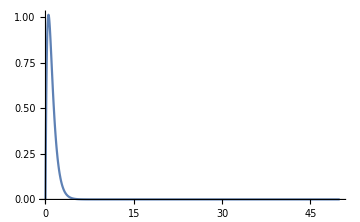

```mathematica
(*AbsoluteTiming@*)Plot[%32f[r]/.eigenfunV[[1]],{r,1.*10^-50,50},ImageSize->Medium,PlotRange->Full]
Plot[%32f[r]/.eigenfunV[[1]],{r,1.*10^-50,2000},ImageSize->Medium,PlotRange->Full]
```

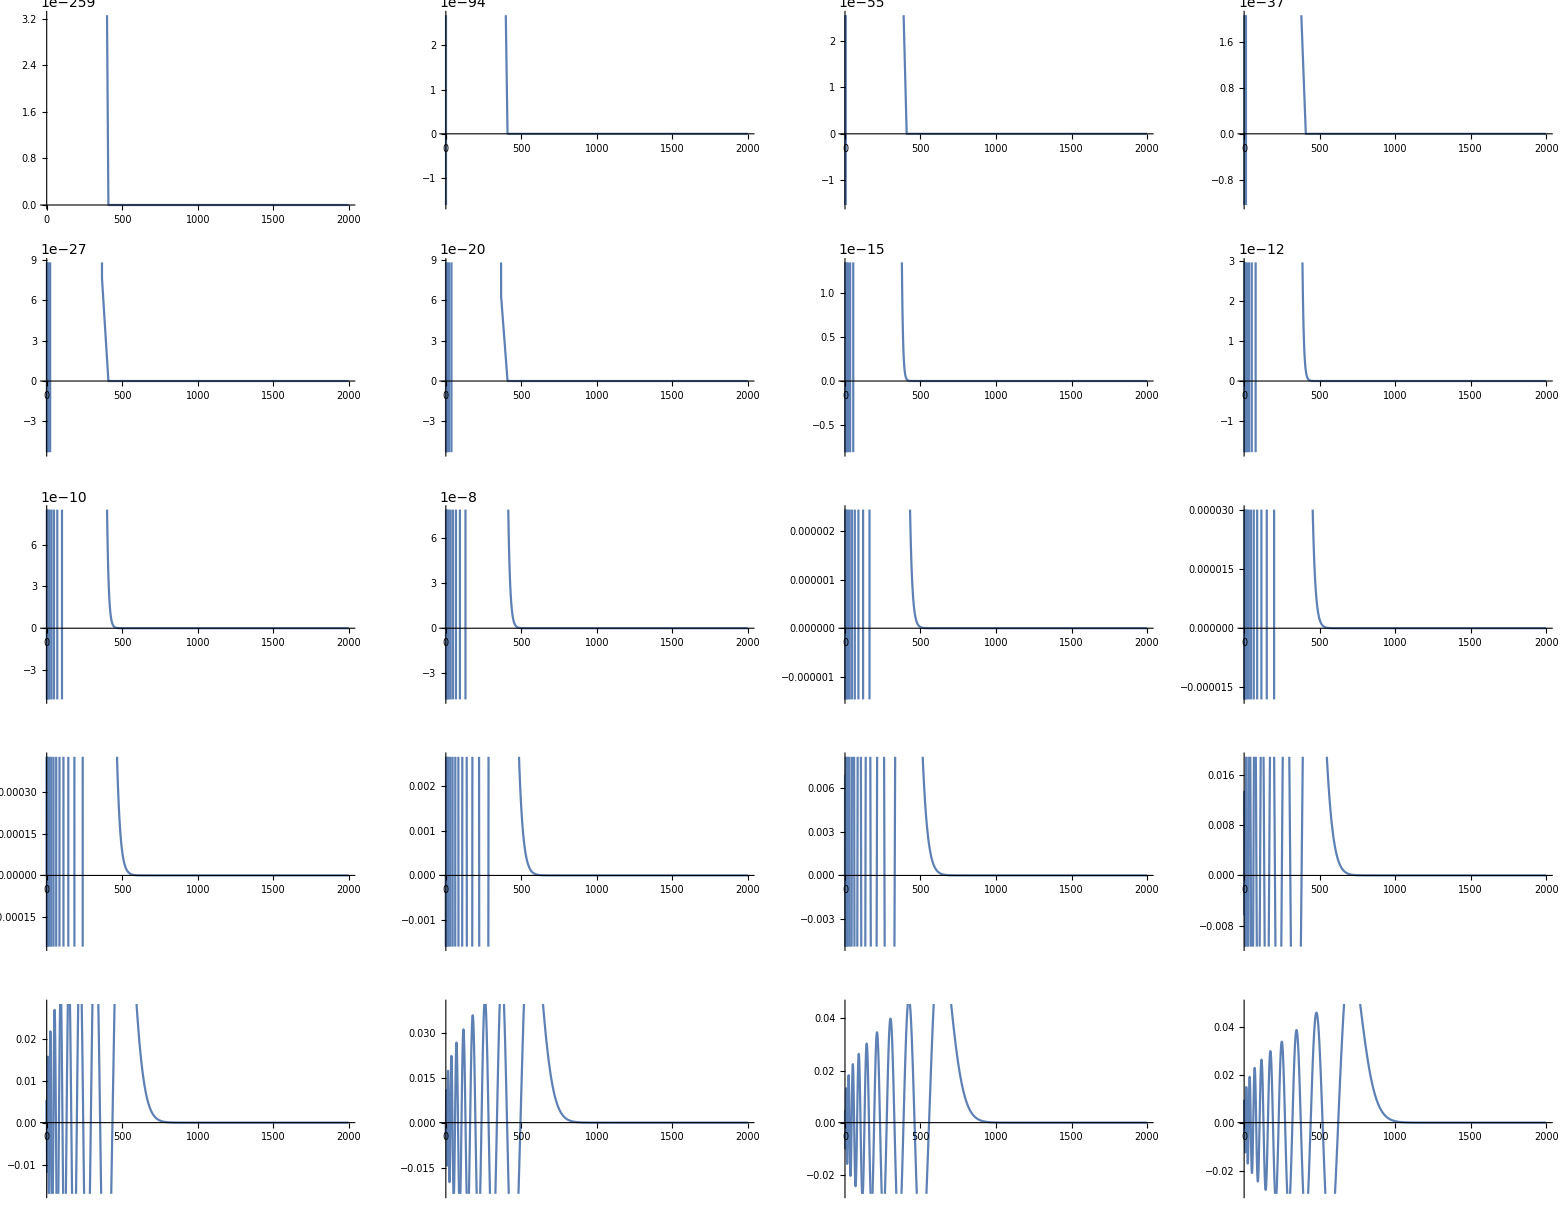

```mathematica
GraphicsGrid@Partition[Plot[am[[#]]f[r]/.eigenfunV[[#]],{r,0,2000},ImageSize->Medium,PlotRange->Full]&/@Range@20,4]
```

```mathematica
NIntegrate[(%32)^2 D[f[r]/.eigenfunV[[1]],{r,2}]^2,{r,1.*10^-50,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]
```

NIntegrate::precw: 参数函数的精度 (1.45240101×10^-2736 (InterpolatingFunction[{{«121»,2000.}},«4»][r])^2) 小于 WorkingPrecision (50.).

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {0.1898740223943864965911995570093489637641431227938723784562868836407957851566662114631488630313222275} 处的 r 中进行 30 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 75.06513254207265928318760354288185786299486325478721494707587432102825046879222492233819028755330482 和 1.672306737862967638015817067865357948024909544545249059668424169748309117201738018444489345423709542×10^-25.

75.065132542072659283187603542881857862994863254787

```mathematica
NIntegrate[am[[#]]^2 D[f[r]/.eigenfunV[[#]],{r,2}]^2,{r,1.*10^-50,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@20
```

NIntegrate::precw: 参数函数的精度 (1.45240101×10^-2736 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466824947118931180812164181631722912×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«200903»},{«1»}}}][r])^2) 小于 WorkingPrecision (50.).

NIntegrate::ncvb: 在接近 {r} = {2.963087378160036820430604510789478477112127410085547906746216381413943966702033044027574534224264122×10^-48} 处的 r 中进行 30 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 2.078899545590398679763513766152758937624351020413197996009644874289982178016511238535488834908628306×10^19 和 1.138213434508340912360437456886436350747859853589099762997888620790709812661887931209398293318526706×10^6.

NIntegrate::precw: 参数函数的精度 (2.90247436756×10^-951 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466824947118931180812164181631722912×10^-51,2000.}},«3»,{{{{2,1},{2,1},{3,2},«46»,{50,49},«200651»},{«1»}}}]«1»«1»])^2) 小于 WorkingPrecision (50.).

NIntegrate::ncvb: 在接近 {r} = {8.682970735082238207881221581307349379552020878482791459432607904503317604711314072911416758217186319×10^-48} 处的 r 中进行 30 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 9.628368901436443733276943845953732685411520279311206818214865285575683658311526305136408140397778319×10^17 和 161882.1679273131043639751017219936239948502666139517795632390885221266869161505724291820728474535055.

NIntegrate::precw: 参数函数的精度 (6.09019737011791×10^-541 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466824947118931180812164181631722912×10^-51,2000.}},«3»,{{{{2,1},{2,1},«47»,{50,49},«200581»},{«1»}}}][r])^2) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NIntegrate::precw 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {r} = {4.921674869329544590788056413324489801870817363841199932083545308701264006289264122266089911730275538×10^-48} 处的 r 中进行 30 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.319328820241394621228445879883632523793010130177467622848111090109613493038707871994774071767467017×10^17 和 8216.00313297182254298193819113144602243489720262705992289086132087587772846125804491927073406515564.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.006761295801710488838195957098457088063730607142023468516995507146749362826027989835945366630605306421 和 1.05743594731209977382507650865417905206085261627554485489267765491882433310424554429257111831969654×10^-10.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.03682085287471629410436294727061767138455413157955096710722221504660028270462887633516187590749177929 和 2.841144387062777243222131341906115288402944033120778928921728603802873025874642354067080515911963757×10^-9.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 0.03062398859594221807701365285610192277250277583231575207788941899056834965116736026321693494061242895 和 2.62050779445853895086921334885795979258538783630386117713759513542342964225769012070657399442629356×10^-9.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{2.0788995455903986797635137661527589376243510204132×10^19,9.6283689014364437332769438459537326854115202793112×10^17,1.3193288202413946212284458798836325237930101301775×10^17,9.1560068295746525312170661410513482002680101562503×10^16,5.7416638216263155316877597150009595849236951557408×10^16,1.5109170357714137131515699456381894658050640384317×10^16,5.2622585138462974302167595134400872182148840375228×10^15,4.3758625885820976586601448798821012167935054054516×10^16,5.991976349865061589335144881798406804133575946509×10^15,4.904842820692172945867466326596092431481529704072×10^16,9.9785401657478446957042671053916295702870402954551×10^15,2.4666773527387613585653437754602347321247954489291×10^15,1.8001589896538358183538842266652135657255233832698×10^16,5.645743106899853141198650609433836038650521642729×10^23,0.0084655822037455653951915497800961910093111607504141,0.0067612958017104888381959570984570880637306071420235,0.036820852874716294104362947270617671384554131579551,0.030623988595942218077013652856101922772502775832316,0.026077092066537995561097536962555195300802613802048,0.022203549635541577455937785377852472828665803045179}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\Dump_Test_eigenfunction_NDSolve_2_withoutnormalization_eigenfunV.mx",eigenfunV]
```